#### Setup

```mathematica
Quiet[<<PhysicalApplications`Astrophysics`GravitationalWaves`InspiralWaves`
<<PhysicalApplications`Astrophysics`GravitationalWaves`Detectors`Detector`
<<PhysicalApplications`Astrophysics`GravitationalWaves`Detectors`Miscellaneous`;
<<PhysicalApplications`Astrophysics`Cosmology`Kinematics`;]
```

--------Retrieving LALInspiralWaveforms.m --------

++ Implement: Injection waveforms: STPN waveforms!

++ Bugs: InspiralTemplate: no orientation? (can't change polarization angle?)
                 hcross implemented manually (complex); check relative factors via inclination.
		 	[assumes HARDCODED NONSPINNING l=|m|=2 amplitude factors]
                 FrequencyComplex  broken (still 1-sided), TimeComplex may pick wrong phase

++ Bugs: TaylorF2 waveform not reconstructed (fourier?)

++ Bugs: alternate sampling rate causes crash.  Currently picks default 2048 Hz

--------Retrieving LALInspiralWaveformsFourierStrainAmplitude.m --------

++ WARNING: PN order convention needs updates!

++ To do:
    - fix: does not evolve when |L|<|S| !  
      Need to insure time refinement then  
    - option to DISABLE r evolution (faster DE solutions for long orbits):
       Add DEMO
    - alternate orders, omega(r) forms.  Options to select different orders (no spin/spin; no quad-monopole)
    - SANE END POINT: evolve to final condition
    - PRECESSION PHASE: track it as well...
    - sanity tests (default; interface with NDSolve tools?: prebuilt BinaryPNS) -> check accuracy/stability
    -
    - apply arbitrary rotations to initial data (default positions, orientations)
    - WAVEFORM EXTRACTION: 0th order, + higher harmonics 
    - hamiltonians?  Use HamiltonanODE tools/symplectic integrators
    - rangewrap output, for safety/use
    - document using L as Lnewtonian
    - poincare sections (via EventLocator) : just in 'demo'?

Debugme: SPA phase expression: confirm agreement (log terms esp)

+++ Aligned spin: Fix amplitude scaling correctly...

++ BUGS: Need to update LAL extractor to sensibly update cutoff frequencies, valid range

--------Retrieving LALMetaio.m --------

--------Retrieving LALInspiralOverlaps.m --------

++LALInspiralWaveformOverlap: 
  Warnings:  Waveforms
     -TaylorF2 broken?! Should not be -- works with raw InspiralOverlap
     -EOBNR crashes link 
  Warnings: Implementation
    - Overlap crashes if parameter seperation too far (memory leak in duration?)

--------Retrieving LALInspiralWaveformsBankEfficiency.m --------

WARNING: This code uses command-line scripts, which generally require properly set environment variables.

WARNING: This code probably only works reliably for l=|m|=2 waveforms (i.e., no inclination effects, spin, multiple harmonics, etc)

--------Retrieving metadataBayesianPostProcessing.m --------

URGENT: Update metadata file to use lookupBindings

WARNING: Recode BayesianPosteriorSamples carefully to use clean dependencies, not duplicated code

++ WARNING: PN order convention needs updates!

++ To do:
    - fix: does not evolve when |L|<|S| !  
      Need to insure time refinement then  
    - option to DISABLE r evolution (faster DE solutions for long orbits):
       Add DEMO
    - alternate orders, omega(r) forms.  Options to select different orders (no spin/spin; no quad-monopole)
    - SANE END POINT: evolve to final condition
    - PRECESSION PHASE: track it as well...
    - sanity tests (default; interface with NDSolve tools?: prebuilt BinaryPNS) -> check accuracy/stability
    -
    - apply arbitrary rotations to initial data (default positions, orientations)
    - WAVEFORM EXTRACTION: 0th order, + higher harmonics 
    - hamiltonians?  Use HamiltonanODE tools/symplectic integrators
    - rangewrap output, for safety/use
    - document using L as Lnewtonian
    - poincare sections (via EventLocator) : just in 'demo'?

Debugme: SPA phase expression: confirm agreement (log terms esp)

+++ Aligned spin: Fix amplitude scaling correctly...

dOperator development: Ok.

DOperator development: Ok.

+++ WARNING: Fisher matrix never debugged to work for log terms.  Does not correctly identify 'J' terms for things without 'f' coefficients though implemented.  Very  important to do the numerical evaluation correctly

+++ WARNING: Take care with evaluating the 'J' expressions...these do not (??) INCLUDE F POWERS? (I thought they did...). debug, make sure amplitude fators included

dOperator development: Ok.

DOperator development: Ok.

Cosmology:Kinematics: Warnings : Assumptions inherent in code only apply at relatively low redshifts z<10^9, so T<<m_e

#### Sanity check: What does f^2 h^2 mean?

The quantity f^2 h^2 has units of  1/area = mass/volume  in dimensionless GR units.  So this is a flux, or equivalently an energy density.

The flux from a point particle is (dE/dt / 4 pi r^2). Roughly speaking, if you add up all the sources in a box ( V* density) and add up all the flux from those sources, you must get the same thing.  


You have already factored everything into the leading-order terms, so you really only need to

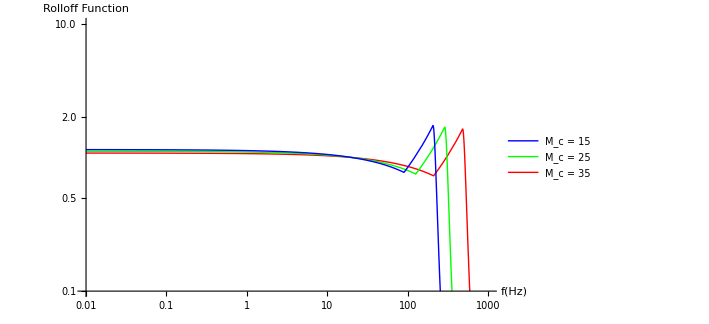

```mathematica
strainAt//Clear
strainAt[MInMsun_,z_?NumberQ,f_?NumberQ] := gwFourierStrainModelFunctionPlanarSymmetry["Phenomenological","IMRPhenomB"][f, (1+z)MInMsun/2,(1+z) MInMsun/2,0,0] (1 Mega Parsec)/PracticalDistanceLuminosity[z]

fref = 20;
zref = 0.01;
LogLogPlot[{((f/fref)^(7/6)strainAt[15 2*2^(1/5),zref,f]/strainAt[15 2*2^(1/5),zref,fref])^2,((f/fref)^(7/6)strainAt[25 2*2^(1/5),zref,f]/strainAt[25 2*2^(1/5),zref,fref])^2,((f/fref)^(7/6)strainAt[35 2*2^(1/5),zref,f]/strainAt[35 2*2^(1/5),zref,fref])^2}, {f,0.01,1000}, PlotRange->{0.1, 10},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Rolloff\nFunction",Black,Bold,25]},TicksStyle->15,ImageSize->525,PlotStyle->{Red,Green,Blue},PlotLegends->Placed[LineLegend[{Blue,Green,Red},{Style["M_c = 15",Black,Bold,20],Style["M_c = 25",Black,Bold,20],Style["M_c = 35",Black,Bold,20]}],{0.45,0.25}]]
```

#### Definitions

```mathematica
c=(SpeedOfLight/( Meter/Second))//SI;(*  3*10^8; *)
M0=(SolarMass/(Meter))//GRUnits;
(*(1.989*10^30 *6.674*10^-11)/c^2*)(*Geometrized Units*)
```

```mathematica
(*Mc^(5/3)(f/c)^(2/3) : Units of meters*)
(*Mc^(5/3)(f/c)^(8/3) : Units of inverse meters*)
F1[Mc_,f_]:=Mc^(5/3) (f/c)^(2/3) UnitStep[1-Mc f/c]
F2[Mc_,f_]:=Mc^(5/3) (f/c)^(2/3)((f/fref)^(7/6)strainAt[Mc 2*2^(1/5)/M0,zref,f]/strainAt[Mc 2*2^(1/5)/M0,zref,fref])^2
PDFm[Mc_]:=1/Mc^2
F1PDFm[Mc_,f_]:=F1[Mc,f]PDFm[Mc]
F2PDFm[Mc_,f_]:=F2[Mc,f]PDFm[Mc]
```

### Plots

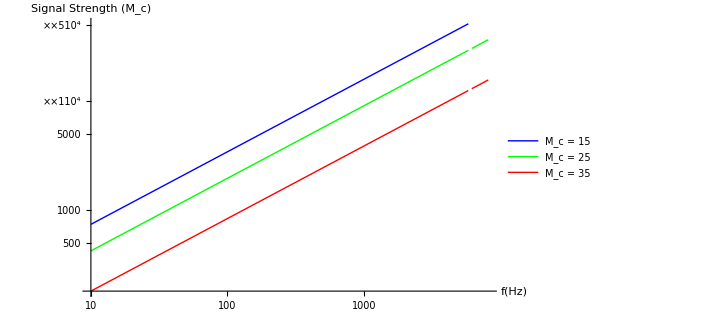

```mathematica
LogLogPlot[{F1[15M0,f],F1[25M0,f],F1[35M0,f]},{f,10^1,10^3.91},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Signal Strength\n(M_c)",Black,Bold,25]},TicksStyle->15,ImageSize->525,PlotRangePadding->.5,PlotStyle->{Red,Green,Blue},PlotLegends->Placed[LineLegend[{Blue,Green,Red},{Style["M_c = 15",Black,Bold,20],Style["M_c = 25",Black,Bold,20],Style["M_c = 35",Black,Bold,20]}],{0.85,0.35}]]
```

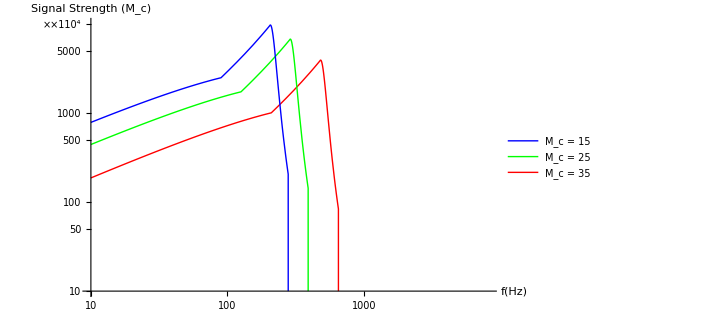

```mathematica
LogLogPlot[{F2[15M0,f]+10^(-9),F2[25M0,f]+10^(-9),F2[35M0,f]+10^(-9)},{f,10^1,10^3.91},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Signal Strength\n(M_c)",Black,Bold,25]},
PlotRange->{10,10^4},TicksStyle->15,ImageSize->525,PlotRangePadding->.5,PlotStyle->{Red,Green,Blue},PlotLegends->Placed[LineLegend[{Blue,Green,Red},{Style["M_c = 15",Black,Bold,20],Style["M_c = 25",Black,Bold,20],Style["M_c = 35",Black,Bold,20]}],{0.85,0.55}]]
```

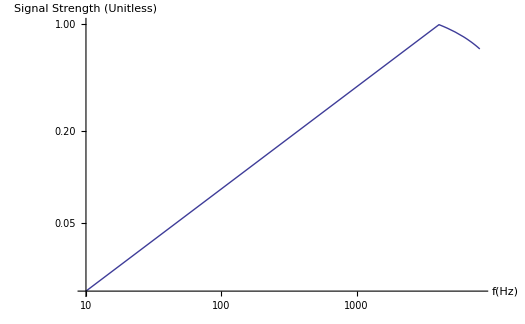

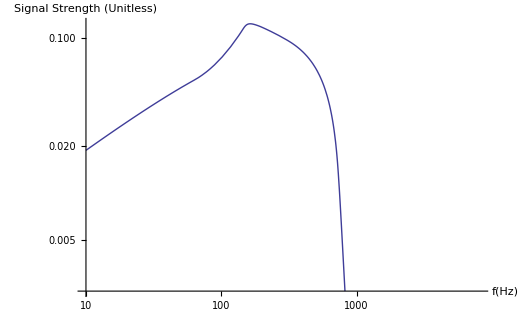

```mathematica
Quiet[LogLogPlot[NIntegrate[F1PDFm[Mc,f],{Mc,10 M0,50 M0}],{f,10^1,10^3.91},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Signal Strength\n(Unitless)",Black,Bold,25]},
TicksStyle->15,ImageSize->525]]
Quiet[LogLogPlot[NIntegrate[F2PDFm[Mc,f],{Mc,10 M0,50 M0}],{f,10^1,10^3.91},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Signal Strength\n(Unitless)",Black,Bold,25]},
TicksStyle->15,ImageSize->525]]
```

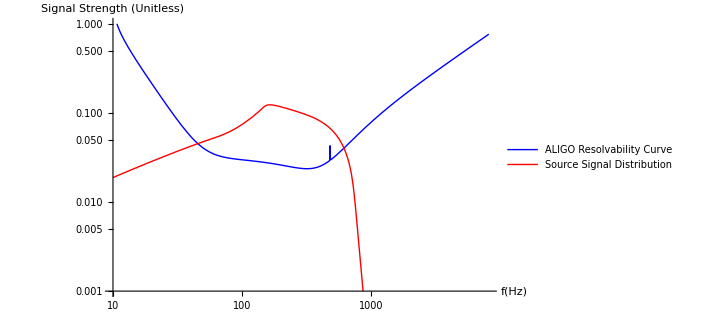

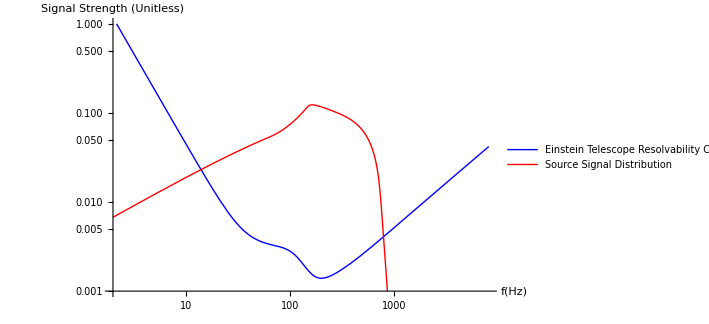

```mathematica
Quiet[LogLogPlot[{(7.481503782142397*^43DetectorSRDFit["AdvancedLIGO"][f])^(1/2),NIntegrate[F2PDFm[Mc,f],{Mc,10 M0,50 M0}]},{f,10,10^3.91},PlotRange->{10^-3,1},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Signal Strength\n(Unitless)",Black,Bold,25]},TicksStyle->15,ImageSize->525,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["ALIGO Resolvability\nCurve",Black,Bold,15],Style["Source Signal Distribution",Black,Bold,15]}],{0.45,0.825}]]]
Quiet[LogLogPlot[{(7.481503782142397*^43DetectorSRDFit["EinsteinTelescope"][f])^(1/2),NIntegrate[F2PDFm[Mc,f],{Mc,10 M0,50 M0}]},{f,10^(.3),10^3.91},PlotRange->{10^-3,1},AxesLabel->{Style["f(Hz)",Black,Bold,25],Style["Signal Strength\n(Unitless)",Black,Bold,25]},TicksStyle->15,ImageSize->525,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{Blue,Red},{Style["Einstein Telescope\nResolvability Curve",Black,Bold,15],Style["Source Signal Distribution",Black,Bold,15]}],{0.55,0.85}]]]
```

```mathematica
Quiet[1/NIntegrate[NIntegrate[F2PDFm[Mc,f],{Mc,10 M0,50 M0}],{f,10,10^3.91}] NIntegrate[If[NIntegrate[F2PDFm[Mc,f],{Mc,10 M0,50 M0}]>(7.481503782142397*^43DetectorSRDFit["AdvancedLIGO"][f])^(1/2),NIntegrate[F2PDFm[Mc,f],{Mc,10 M0,50 M0}]-(7.481503782142397*^43DetectorSRDFit["AdvancedLIGO"][f])^(1/2),0],{f,10,10^3.91}]]
Quiet[1/NIntegrate[NIntegrate[F2PDFm[Mc,f],{Mc,10 M0,50 M0}],{f,10^(.3),10^3.91}] NIntegrate[If[NIntegrate[F2PDFm[Mc,f],{Mc,10 M0,50 M0}]>(7.481503782142397*^43DetectorSRDFit["EinsteinTelescope"][f])^(1/2),NIntegrate[F2PDFm[Mc,f],{Mc,10 M0,50 M0}]-(7.481503782142397*^43DetectorSRDFit["EinsteinTelescope"][f])^(1/2),0],{f,10^(.3),10^3.91}]]
```

0.588088

0.950845

```mathematica
Solve[M==((m^2)^(3/5))/(2m)^(1/5),m]
```

{{m→-(-2)^(1/5) M},{m→2^(1/5) M},{m→(-1)^(2/5) 2^(1/5) M},{m→-(-1)^(3/5) 2^(1/5) M},{m→(-1)^(4/5) 2^(1/5) M}}